#### code below generates left panel of Figure 2

```mathematica
ClearAll["Global`*"]
sreq[tt_,τ_,tlr_,t0r_,a_,b_,δ_,d_,da_,l_,σ_,α_,ϵ_,γ_,0]:=sreq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,0]=10^7;
j[t_,tlx_,t0x_]:=If[t0x<t<(tlx+t0x),1/tlx,0];
sreq[tt_?NumericQ,τ_?NumericQ,tlr_?NumericQ,t0r_?NumericQ,a_,b_,δ_,d_,da_,l_,σ_,α_,ϵ_,γ_,n_]:=sreq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n]=
(sol=NDSolve[{
D[s1[t], t]==sreq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n-1]* j[t,tlr,t0r]-d* s1[t]-a *s1[t]*v1[t]-l s1[t],
D[s2[t], t]==l s1[t]-da s2[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a b*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,s2[t/;t≤0]==0,v1[t/;t≤0]==veq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n-1],v2[t/;t≤0]==0},{s1,s2,v1,v2},{t,0,tt}];
sreq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n] =First@Evaluate[ϵ σ s2[tt]/(1+ α s2[tt])/.sol]);
veq[tt_,τ_,tlr_,t0r_,a_,b_,δ_,d_,da_,l_,σ_,α_,ϵ_,γ_,0]:=veq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,0]=1;
j[t_,tlx_,t0x_]:=If[t0x<t<(tlx+t0x),1/tlx,0];
veq[tt_?NumericQ,τ_?NumericQ,tlr_?NumericQ,t0r_?NumericQ,a_,b_,δ_,d_,da_,l_,σ_,α_,ϵ_,γ_,n_]:=veq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n]=
(sol=NDSolve[{
D[s1[t], t]==sreq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n-1]* j[t,tlr,t0r]-d* s1[t]-a *s1[t]*v1[t]-l s1[t],
D[s2[t], t]==l s1[t]-da s2[t],
D[v1[t], t]==-δ v1[t],
D[v2[t], t]== a b*Exp[-d τ]s1[t-τ]*v1[t-τ]-δ v2[t],
s1[t/;t≤0]==0,s2[t/;t≤0]==0,v1[t/;t≤0]==veq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n-1],v2[t/;t≤0]==0},{s1,s2,v1,v2},{t,0,tt}];
veq[tt,τ,tlr,t0r,a,b,δ,d,da,l,σ,α,ϵ,γ,n] =γ First@Evaluate[v2[tt]/.sol]);
```

no parasites

```mathematica
liste=Table[{tlx,t0x,s0=10^7; v0=1; sr=sreq[tt,τ,tlx,t0x,a,b,δ,d,da,l,σ,α,ϵ,γ,100]/.{tt->4,τ->3,a->10^-6,b->0,δ->2,d->0.2,da->0.015,l->1, α->0.0001, σ->600,ϵ->0.85,γ->0.9 };sr},{tlx,0.5,3,0.1},{t0x,0,2,0.1}];
```

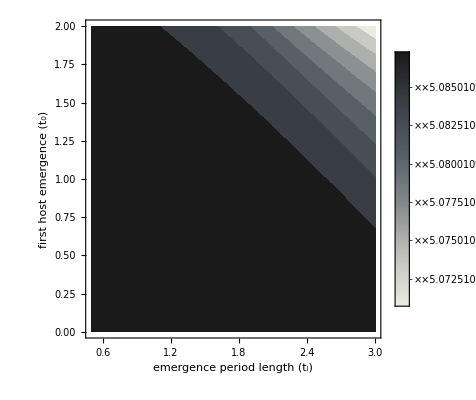

```mathematica
ListContourPlot[Flatten[liste,1],ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotLegends->Placed[BarLegend[Automatic,None, LegendLabel->Style["H^*",30,Black,FontFamily->"Times"],LegendMarkerSize->{25,225},LabelStyle->{FontSize->18,FontFamily->"Times"}],Right],Contours->8,FrameTicksStyle->Directive[FontSize->18,Opacity[0],FontOpacity->1],FrameStyle->Thickness[.002],FrameLabel->{{Style["first host emergence (t_0)",22,Black],None},{Style["emergence period length (t_l)",22,Black],Style["without parasites",22,Black]}},LabelStyle->Directive[Bold,FontFamily->"Times"],ContourStyle->None,PlotRange->All]
```

very early emergence is maladaptive because adults can die before the end of the season

```mathematica
listp=Table[{tlx,t0x,s0=10^7; v0=1; sr=sreq[tt,τ,tlx,t0x,a,b,δ,d,da,l,σ,α,ϵ,γ,100]/.{tt->4,τ->2,a->10^-6,b->400,δ->2,d->0.2,da->0.015,l->1, α->0.0001, σ->600,ϵ->0.85,γ->0.9 };sr},{tlx,0.5,3,0.1},{t0x,0,2,0.1}];
```

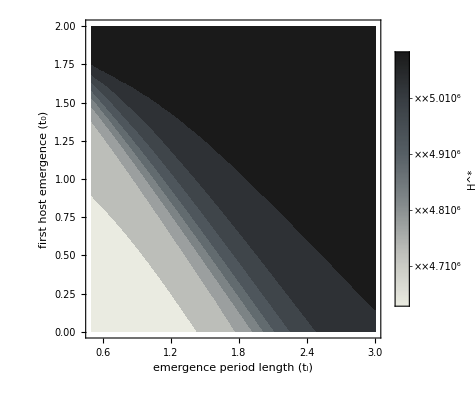

```mathematica
ListContourPlot[Flatten[listp,1],ColorFunction->ColorData[{"GrayTones","Reverse"}],PlotLegends->Placed[BarLegend[Automatic,None, LegendLabel->Style["H^*",30,Black,FontFamily->"Times"],LegendMarkerSize->{25,225},LabelStyle->{FontSize->18,FontFamily->"Times"}],Right],Contours->8,FrameTicksStyle->Directive[FontSize->18,Opacity[0],FontOpacity->1],FrameStyle->Thickness[.002],FrameLabel->{{Style["first host emergence (t_0)",22,Black],None},{Style["emergence period length (t_l)",22,Black],Style["with parasites",22,Black]}},LabelStyle->Directive[Bold,FontFamily->"Times"],ContourStyle->None,PlotRange->All]
```

#### code below generates left panel of Figure 3

```mathematica
ClearAll["Global`*"]
xv[T_,tl_,t0_,τ_,a_,δ_,d_,da_, b_,l_, ρ_,α_,ϵ_,γ_,0]:=xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,0]=1;
j[t_,tlx_,t0x_]:=If[t0x<t<(tlx+t0x),1/tlx,0];
xv[T_,tl_,t0_,τ_?NumericQ,a_,δ_,d_,da_, b_,l_, ρ_,α_,ϵ_,γ_,n_]:=xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n]=
(solv=NDSolve[{
D[s1[t], t]==xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n-1]* j[t,tl,t0]-d* s1[t]-a *s1[t]*v[t]-l s1[t],
D[s2[t], t]==l s1[t]-da* s2[t],
D[v[t], t]== a b*Exp[-d τ]s1[t-τ]*v[t-τ]-δ v[t],
s1[t/;t≤0]==0,s2[t/;t≤0]==0,v[t/;t≤0]==xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n-1]},{v},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
xv[T,tl,t0,τ,a,δ,d, da,b,l,ρ,α,ϵ,γ,n] =γ First@Evaluate[v[T]/.solv]);
xs[T_,tl_,t0_,τ_,a_,δ_,d_,da_, b_,l_, ρ_,α_,ϵ_,γ_,0]:=xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,0]=10^7;
xs[T_,tl_,t0_,τ_?NumericQ,a_,δ_,d_,da_, b_,l_, ρ_,α_,ϵ_,γ_,n_]:=xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n]=
(sols=NDSolve[{
D[s1[t], t]==xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n-1]* j[t,tl,t0]-d* s1[t]-a *s1[t]*v[t]-l s1[t],
D[s2[t], t]==l s1[t]-da* s2[t],
D[v[t], t]== a b*Exp[-d τ]s1[t-τ]*v[t-τ]-δ v[t],
s1[t/;t≤0]==0,s2[t/;t≤0]==0,v[t/;t≤0]==xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n-1]},{s2},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n]=First@Evaluate[(ϵ ρ s2[T]/(1+α s2[T]))/.sols])
j[t_,tlx_,t0x_]:=If[t0x<t<(tlx+t0x),1/tlx,0];
```

```mathematica
sol[s0_,v0_,T_,tl_,t0_,τ_?NumericQ,a_,δ_,d_,da_, b_,l_, ρ_,α_]:=NDSolve[{
D[s1[t], t]==s0* j[t,tl,t0]-d* s1[t]-a *s1[t]*v[t]-l s1[t],
D[s2[t], t]==l s1[t]-da* s2[t],
D[i[t], t]==a *s1[t]*v1[t]-d* i[t],
D[dd[t], t]==d* s1[t],
D[v[t], t]== a b*Exp[-d τ]s1[t-τ]*v[t-τ]-δ v[t],
D[v1[t], t]== -δ v1[t],
s1[t/;t≤0]==0,s2[t/;t≤0]==0,i[t/;t≤0]==0,dd[t/;t≤0]==0,v[t/;t≤0]==v0,v1[t/;t≤0]==v0},{s1,s2,i,dd,v,v1},{t,0,T}];
```

with parasites, t_0 = 0; t_l = 0.5;

```mathematica
τ=3; T=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
```

```mathematica
t0=0;tl=0.5;τ=3;b=400;
s0=xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
v0=xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
```

3.14381×10^6

1.6207×10^8

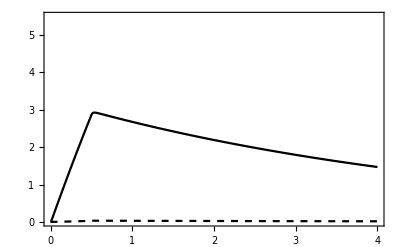
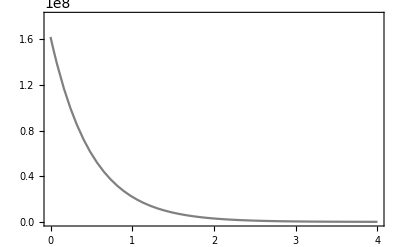

```mathematica
p1=Plot[{Evaluate[s2[t]/.sol[s0,v0,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],Evaluate[i[t]/.sol[s0,v0,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,False},FrameLabel->{{Style["",16],None},{None,Style["with parasites",16]}},PlotRange->{{0,4},{0,5.5*10^6}}];
p2=Plot[Evaluate[v1[t]/.sol[s0,v0,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],{t,0,4},Axes->None,PlotStyle->{Gray},BaseStyle->{FontSize->14},FrameTicks->{{None,{{0,"0"},{0.5*10^8,"0.5"},{1*10^8,"1.0"},{1.5*10^8,"1.5"}}},{None,None}},ImagePadding->{{80,95},{50,50}},Frame->{False,False,False,True},FrameLabel->{{None,Rotate[Style["",16],180 Degree]},{None,None}},PlotRange->{{0,4},{0,1.8*10^8}}];
p=Overlay[{p1,p2}]
```

```mathematica
t0=0;tl=0.5;
s002=xs[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
v002=xv[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
```

5.07832×10^6

0.

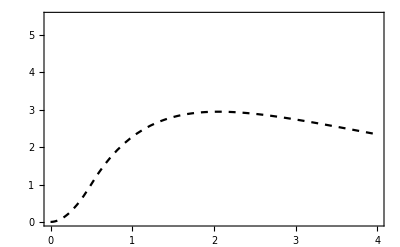

```mathematica
pnp1=Plot[{Evaluate[s2[t]/.sol[s002,v002,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dotted,Black],Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,True},FrameLabel->{{Style["",16],None},{None,Style["without parasites",16]}},PlotRange->{{0,4},{0,5.5*10^6}}]
```

with parasites, t_0 = 0.917; t_l = 0.5;

```mathematica
t0=0.917;tl=0.5;τ=3;b=400;
s01=xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
v01=xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
```

5.08127×10^6

5.30763

parasites are nearly driven extinct at the adaptive timing of first host emergence

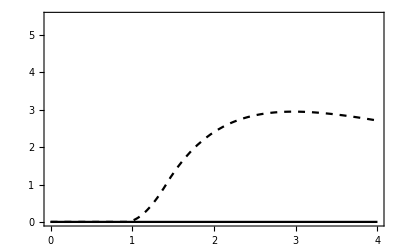
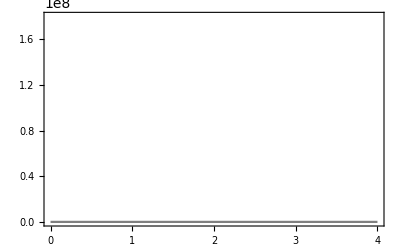

```mathematica
p1=Plot[{Evaluate[s2[t]/.sol[s01,v01,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],Evaluate[i[t]/.sol[s01,v01,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,False},FrameLabel->{{Style["",16],None},{None,None}},PlotRange->{{0,4},{0,5.5*10^6}}];
p2=Plot[Evaluate[v[t]/.sol[s01,v01,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],{t,0,4},Axes->None,PlotStyle->{Gray},BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},Frame->{False,False,False,True},FrameTicks->{{None,{{0,"0"},{0.5*10^8,"0.5"},{1*10^8,"1.0"},{1.5*10^8,"1.5"}}},{None,None}},FrameLabel->{{None,Rotate[Style["",16],180 Degree]},{None,None}},PlotRange->{{0,4},{0,1.8*10^8}}];
p=Overlay[{p1,p2}]
```

without parasites, t_0 = 0..917; t_l = 0.5;

```mathematica
t0=0.917;tl=0.5;b=0;
s002=xs[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
v002=xv[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
```

5.08127×10^6

0.

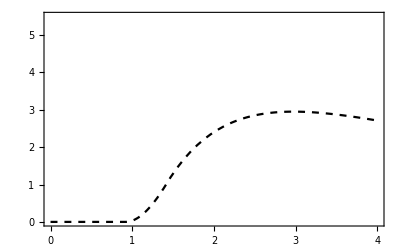

```mathematica
pnp2=Plot[{Evaluate[s2[t]/.sol[s002,v002,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dotted,Black],Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,True},FrameLabel->{{Style["",16],None},{None,None}},PlotRange->{{0,4},{0,5.5*10^6}}]
```

with parasites, t_0 = 0; t_l = 2.89 ;

t_l^* = 2.89 when τ = 3

```mathematica
t0=0;tl=2.89;τ=3;b=400;
s02=xs[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
v02=xv[T,tl,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]
```

5.01375×10^6

1.51814×10^8

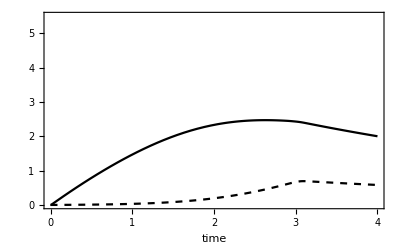
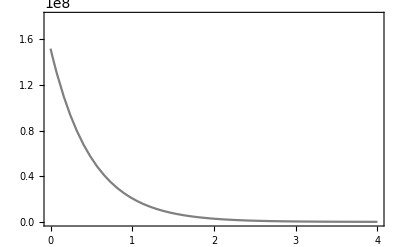

```mathematica
p1=Plot[{Evaluate[s2[t]/.sol[s02,v02,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],Evaluate[i[t]/.sol[s02,v02,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,False},FrameLabel->{{Style["",16],None},{Style["time",16],None}},PlotRange->{{0,4},{0,5.5*10^6}}];
p2=Plot[Evaluate[v1[t]/.sol[s02,v02,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]],{t,0,4},Axes->None,PlotStyle->{Gray},BaseStyle->{FontSize->14},FrameTicks->{{None,{{0,"0"},{0.5*10^8,"0.5"},{1*10^8,"1.0"},{1.5*10^8,"1.5"}}},{None,None}},ImagePadding->{{80,95},{50,50}},Frame->{False,False,False,True},FrameLabel->{{None,Rotate[Style["",16],180 Degree]},{None,None}},PlotRange->{{0,4},{0,1.8*10^8}}];
p=Overlay[{p1,p2}]
```

without parasites, t_0 = 0; t_l = 2.89 ;

```mathematica
t0=0;tl=2.89;τ=3;
s003=xs[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
v003=xv[T,tl,t0,τ,a,δ,d,da, 0,l,ρ,α,ϵ,γ,150]
```

5.08129×10^6

1.×10^-323

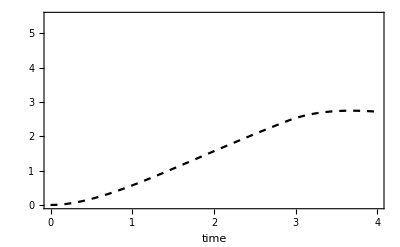

```mathematica
pnp3=Plot[{Evaluate[s2[t]/.sol[s003,v003,T,tl,t0,τ,a,δ,d,da, b,l,ρ,α]]},{t,0,4},PlotStyle->{Directive[Dotted,Black],Directive[Dashed,Black],Black},Axes->None,BaseStyle->{FontSize->14},ImagePadding->{{80,95},{50,50}},FrameTicks->{{{{0,"0"},{1*10^6,"1"},{2*10^6,"2"},{3*10^6,"3"},{4*10^6,"4"},{5*10^6,"5"}},None},{{0,1,2,3,4},None}},Frame->{True,True,True,True},FrameLabel->{{Style["",16],None},{Style["time",16],None}},PlotRange->{{0,4},{0,5.5*10^6}}]
```

#### code below generates left panel of Figure 4 (method is described in Appendix C)

```mathematica
xsm[T_,tlr_?NumericQ,tlm_?NumericQ,t0r_?NumericQ,t0m_?NumericQ,τ_?NumericQ,a_,δ_,d_,da_, b_,l_, ρ_,α_,ϵ_,γ_,n_]:=
(solm=NDSolve[{
D[s1r[t], t]==xs[T,tlr,t0r,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n]* j[t,tlr,t0r]-d* s1r[t]-a *s1r[t]*v[t]-l s1r[t],
D[s1m[t], t]== j[t,tlm,t0m]-d* s1m[t]-a *s1m[t]*v[t]-l s1m[t],
D[s2r[t], t]==l s1r[t]-da* s2r[t],
D[s2m[t], t]==l s1m[t]-da* s2m[t],
D[v[t], t]== a b*Exp[-d τ](s1r[t-τ]+s1m[t-τ])*v[t-τ]-δ v[t],
s1r[t/;t≤0]==0,s1m[t/;t≤0]==0,s2r[t/;t≤0]==0,s2m[t/;t≤0]==0,v[t/;t≤0]==xv[T,tlr,t0r,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,n]},{s2r,s2m},{t,0,T},MaxStepSize->10^1000,Method->{"StiffnessSwitching"},MaxSteps->10^6,WorkingPrecision->MachinePrecision];
s0m =First@Evaluate[ϵ ρ s2m[T]/(1+ α (s2r[T]+s2m[T]))/.solm])
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
Table[
esslist0g=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0.4,2.4,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={τx,First@zz},{τx,1,3.5,0.25}]
```

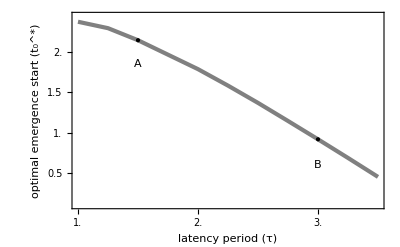

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.03,0}}&/@Range[1,3.5,0.5],None}};
xx=ListLinePlot[{esslist0g},Frame->{{True,True},{True,True}},PlotRange->{{1,3.5},{0.1,2.45}},FrameTicks->ftrange,PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n start (t_0^*)",16,FontFamily->"Helvetica"],None},{Style["latency period (τ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True,Epilog->{Black,PointSize[Large], Point[{1.5,2.15}],Black,PointSize[Large], Point[{3,0.91}],Style[Text["A",{1.5,1.85}],18,FontFamily->"Times"],Style[Text["B",{3,0.6}],18,FontFamily->"Times"]}]
```

```mathematica
tl=0.5; τ=1.5; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
slisttl=Table[{t0x,xs[Tx,tl,t0x,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{t0x,0,2.3,0.1}];
```

```mathematica
tl=0.5;τ=1.5;b=400;t0x=2.15;
stless={{t0x,xs[Tx,tl,t0x,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]}}
```

{{2.15,5.08264×10^6}}

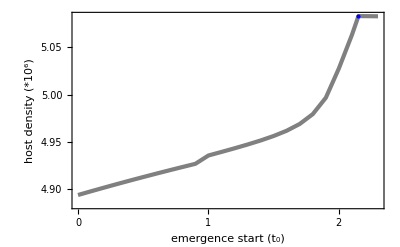

```mathematica
ListLinePlot[slisttl,Frame->True,FrameLabel->{{Style["host density (*10^6)",20,FontFamily->"Helvetica"],None},{Style["emergence start (t_0)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{3*10^6,"3.0"},{3.5*10^6,"3.5"},{4*10^6,"4.0"},{4.5*10^6,"4.5"},{5*10^6,"5.0"}},None},{{0,0.5,1,1.5,2,2.5,3},None}},PlotStyle->{Directive[Black,Opacity[0.5]]},PlotRange->{{0,2.3},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stless]}]
```

```mathematica
tl=0.5; τ=1.5; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
vlistt0=Table[{t0x,xv[Tx,tl,t0x,τ,a,δ,da, b,l,ρ,α,ϵ,γ,150]},{t0x,0,2.3,0.1}];
```

```mathematica
tl=0.5;τ=1.5;b=400;t0x=2.15;
vtless={{t0x,xv[Tx,tl,t0x,τ,a,δ,d, da, b,l,ρ,α,ϵ,γ,150]}};
```

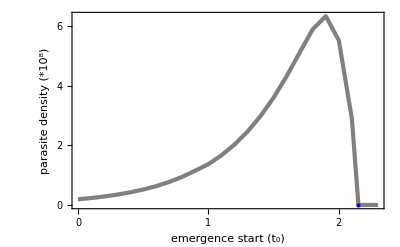

```mathematica
ListLinePlot[vlistt0,Frame->True,FrameLabel->{{Style["parasite density (*10^8)",20,FontFamily->"Helvetica"],None},{Style["emergence start (t_0)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{0,"0"},{2*10^8,"2"},{4*10^8,"4"},{6*10^8,"6"}},None},{{0,0.5,1,1.5,2,2.5,3},None}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0,2.3},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[vtless]}]
```

```mathematica
tl=0.5; τ=3; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
slisttl=Table[{t0x,xs[Tx,tl,t0x,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{t0x,0,2.3,0.1}];
```

```mathematica
tl=0.5;τ=3;b=400;t0x=0.917;
stless={{t0x,xs[Tx,tl,t0x,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]}};
```

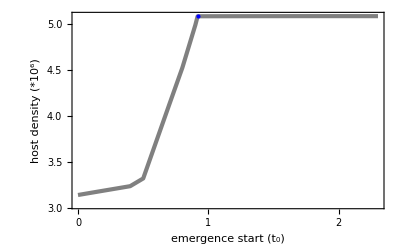

```mathematica
ListLinePlot[slisttl,Frame->True,FrameLabel->{{Style["host density (*10^6)",20,FontFamily->"Helvetica"],None},{Style["emergence start (t_0)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicks->{{{{3*10^6,"3.0"},{3.5*10^6,"3.5"},{4*10^6,"4.0"},{4.5*10^6,"4.5"},{5*10^6,"5.0"}},None},{{0,0.5,1,1.5,2,2.5,3},None}},FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},PlotStyle->{Directive[Black,Opacity[0.5]]},PlotRange->{{0,2.3},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stless]}]
```

```mathematica
tl=0.5; τ=3; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
vlistt0=Table[{t0x,xv[Tx,tl,t0x,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{t0x,0,2.3,0.1}];
```

```mathematica
tl=0.5;τ=3;b=400;t0x=0.917;
vtless={{t0x,xv[Tx,tl,t0x,τ,a,δ,d, da, b,l,ρ,α,ϵ,γ,40]}};
```

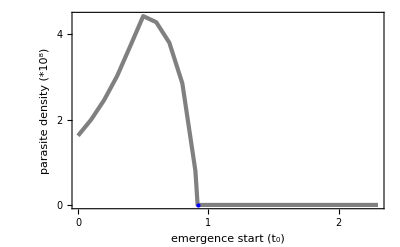

```mathematica
ListLinePlot[vlistt0,Frame->True,FrameLabel->{{Style["parasite density (*10^8)",20,FontFamily->"Helvetica"],None},{Style["emergence start (t_0)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{0,"0"},{2*10^8,"2"},{4*10^8,"4"},{6*10^8,"6"}},None},{{0,0.5,1,1.5,2,2.5,3},None}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0,2.3},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[vtless]}]
```

#### code below generates left panel of Figure 5 (method is described in Appendix C)

```mathematica
τ=1;Tx=4;t0rx=t0mx=0;b=400;
Table[list=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τx,a,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.8,3.4,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={τx,First@zz},{τx,1,3.5,0.25}]
```

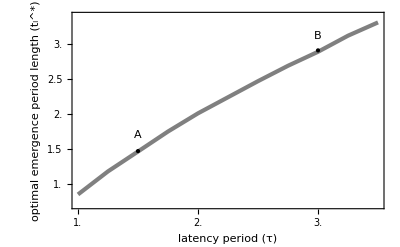

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,0.5],None},{{#,#,{0.03,0}}&/@Range[1,3.5,0.5],None}};
xx=ListLinePlot[{esslistl},Frame->{{True,True},{True,True}},PlotRange->{{1,3.5},{0.7,3.4}},FrameTicks->ftrange,PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n period length (t_l^*)",16,FontFamily->"Helvetica"],None},{Style["latency period (τ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True,Epilog->{Black,PointSize[Large], Point[{1.5,1.47}],Black,PointSize[Large], Point[{3,2.91}],Style[Text["A",{1.5,1.7}],18,FontFamily->"Times"],Style[Text["B",{3,3.12}],18,FontFamily->"Times"]}]
```

```mathematica
t0=0; τ=1.5; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9;
slisttl=Table[{tlx,xs[4,tlx,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{tlx,0.5,3.2,0.1}];
```

```mathematica
t0=0;τ=1.5;b=400;tls=1.464;
stless={{tls,xs[4,tls,t0,τ,a,δ,d, da, b,l,ρ,α,ϵ,γ,150]}};
```

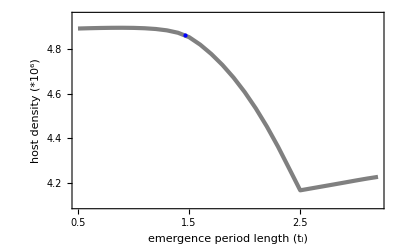

```mathematica
ListLinePlot[slisttl,Frame->True,FrameLabel->{{Style["host density (*10^6)",20,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{4.2*10^6,"4.2"},{4.4*10^6,"4.4"},{4.6*10^6,"4.6"},{4.8*10^6,"4.8"}},None},{{0.5,1,1.5,2,2.5,3},None}},PlotStyle->{Directive[Black,Opacity[0.5]]},PlotRange->{{0.5,3.2},{4.1*10^6,4.95*10^6}},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stless]}]
```

```mathematica
t0=0; τ=1.5; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85; γ=0.9;
vlisttl=Table[{tlx,xv[4,tlx,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{tlx,0.5,3.2,0.1}];
```

```mathematica
t0=0;τ=1.5;b=400;tls=1.464;
stlessv={{tls,xv[4,tls,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]}};
```

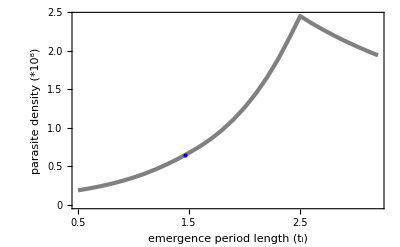

```mathematica
ListLinePlot[vlisttl,Frame->True,FrameLabel->{{Style["parasite density (*10^8)",20,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{2.5*10^8,"2.5"},{2*10^8,"2.0"},{1*10^8,"1.0"},{1.5*10^8,"1.5"},{0.5*10^8,"0.5"},{0,"0"}},None},{{0.5,1,1.5,2,2.5,3},None}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0.5,3.2},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stlessv]}]
```

```mathematica
t0=0; τ=3; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85; γ=0.9;
slisttl=Table[{tlx,xs[4,tlx,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]},{tlx,0.5,3.2,0.1}];
```

```mathematica
t0=0;τ=3;b=400;tls=2.89;
stless={{tls,xs[4,tls,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]}};
```

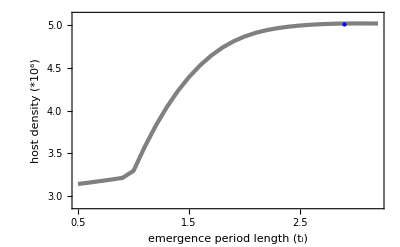

```mathematica
ListLinePlot[slisttl,Frame->True,FrameLabel->{{Style["host density (*10^6)",20,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{3*10^6,"3.0"},{3.5*10^6,"3.5"},{4*10^6,"4.0"},{4.5*10^6,"4.5"},{5*10^6,"5.0"}},None},{{0.5,1,1.5,2,2.5,3},None}},PlotStyle->{Directive[Black,Opacity[0.5]]},PlotRange->{{0.5,3.2},{2.9*10^6,5.1*10^6}},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stless]}]
```

```mathematica
t0=0; τ=3; Tx=4; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85; γ=0.9;
vlisttl=Table[{tlx,xv[4,tlx,t0,τ,a,δ,d, da, b,l,ρ,α,ϵ,γ,150]},{tlx,0.5,3.2,0.1}];
```

```mathematica
t0=0;τ=3;b=400;tls=2.89;
stlessv={{tls,xv[4,tls,t0,τ,a,δ,d,da, b,l,ρ,α,ϵ,γ,150]}};
```

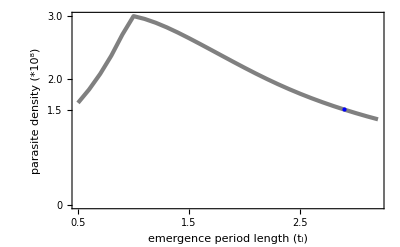

```mathematica
ListLinePlot[vlisttl,Frame->True,FrameLabel->{{Style["parasite density (*10^8)",20,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",20,FontFamily->"Helvetica"],None}},PlotStyle->{{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{16,FontFamily->"Helvetica"},{16,FontFamily->"Helv|etica"}},FrameTicks->{{{{3*10^8,"3.0"},{2.5*10^8,"2.5"},{2*10^8,"2.0"},{1*10^8,"1.0"},{1.5*10^8,"1.5"},{0.5*10^8,"0.5"},{0,"0"}},None},{{0.5,1,1.5,2,2.5,3},None}},PlotStyle->Directive[Black,Opacity[0.5]],PlotRange->{{0.5,3.2},All},FrameStyle->18,Epilog->{PointSize[Large],Blue,Point[stlessv]}]
```

#### code below generates figures in Appendix D

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; ax=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9; τ=1.5;
Table[
esslist0g=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={ax,First@zz},{ax,0.000001,0.007,0.0001}]
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; ax=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ρ=600; ϵ=0.85;γ=0.9; τ=3;
Table[
esslist0g3=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={ax,First@zz},{ax,0.000001,0.007,0.0001}]
```

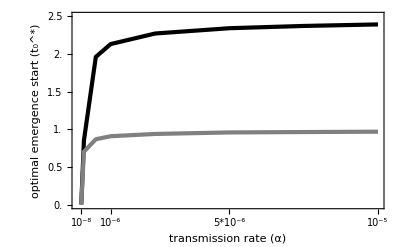

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.03,0}}&/@Range[1/100000000,1/100000,1/10000],None}};
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{-.00000010,1/100000},{0,2.5}},FrameTicks->{{{#,#,{0.03,0}}&/@Range[0,2.5,0.5],None},{{{1/100000000,"10^-8"},{1/1000000,"10^-6"},{5*10^-6,"5*10^-6"},{1/100000,"10^-5"}},None}},PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n start (t_0^*)",16,FontFamily->"Helvetica"],None},{Style["transmission rate (α)",16,FontFamily->"Helvetica"],None}},RotateLabel->True]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=1.5;
Table[esslist0g=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={ax,First@zz},{ax,0.000001,0.007,0.0001}]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=3;
Table[esslist0g3=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,ax,δ,d,da, b,l,ρ,α,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={ax,First@zz},{ax,0.000001,0.007,0.0001}]
```

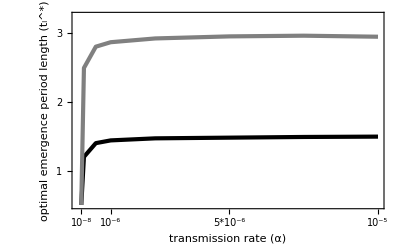

```mathematica
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{-.00000010,1/100000},{0.5,3.25}},FrameTicks->{{{#,#,{0.03,0}}&/@Range[0,3,1],None},{{{1/100000000,"10^-8"},{1/1000000,"10^-6"},{5*10^-6,"5*10^-6"},{1/100000,"10^-5"}},None}},PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n period length (t_l^*)",16,FontFamily->"Helvetica"],None},{Style["transmission rate (α)",16,FontFamily->"Helvetica"],None}},RotateLabel->True]
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ϵ=0.85;γ=0.9; τ=1.5;
Table[
esslist0g=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={ρx,First@zz},{ρx,10,1000,50}]
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  α=0.0001; ϵ=0.85;γ=0.9; τ=3;
Table[
esslist0g3=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={ρx,First@zz},{ρx,10,1000,50}]
```

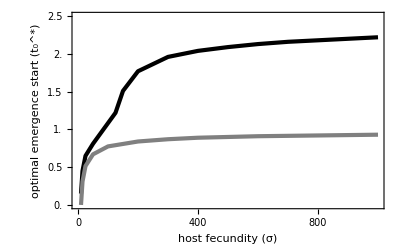

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,2.5,0.5],None},{{#,#,{0.03,0}}&/@Range[0,1000,200],None}};
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{0,1000},{0,2.5}},FrameTicks->ftrange,PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n start (t_0^*)",16,FontFamily->"Helvetica"],None},{Style["host fecundity (σ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=1.5;
Table[esslist0g=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={ρx,First@zz},{ρx,10,1000,50}]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=3;
Table[esslist0g3=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρx,α,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={ρx,First@zz},{ρx,10,1000,50}]
```

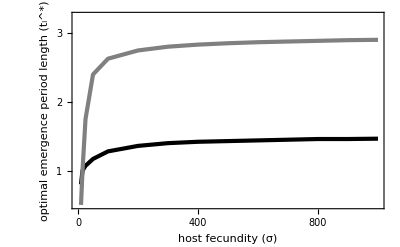

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,3,1],None},{{#,#,{0.03,0}}&/@Range[0,1000,200],None}};
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{0,1000},{0.5,3.25}},FrameTicks->ftrange,PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n period length (t_l^*)",16,FontFamily->"Helvetica"],None},{Style["host fecundity (σ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True]
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  ϵ=0.85;γ=0.9; τ=1.5;
Table[
esslist0g=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={αx,First@zz},{αx,0.000001,0.007,0.0005}]
```

```mathematica
Tx=4; tlrx=tlmx=0.5; b=400; a=10^-6; b=400; δ=2; d=0.2; da=0.015; l=1;  ϵ=0.85;γ=0.9; τ=3;
Table[
esslist0g3=Table[{t0rx,x=xsm[Tx,tlrx,tlmx,t0rx,t0rx+0.01,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300];(*mutant density w/ t0m = t0r + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlmx,t0rx,t0rx-0.01,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300];
(*mutant density w/ w/ t0m = t0r - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx+0.01,t0rx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx,tlmx,t0rx-0.01,t0rx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,300]];
(*w and z are used to determine if mutual invasion occurs between t0rx and t0rx +/- 0.01,mutual invasion implies that the ess is in between t0rx and t0rx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{t0rx,0,1.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out1={αx,First@zz},{αx,0.000001,0.007,0.0005}]
```

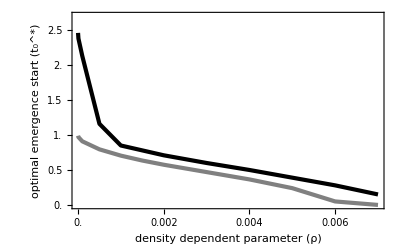

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,2.7,0.5],None},{{#,#,{0.03,0}}&/@Range[0,0.007,0.002],None}};
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{0,0.007},{0,2.7}},FrameTicks->ftrange,PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n start (t_0^*)",16,FontFamily->"Helvetica"],None},{Style["density dependent parameter (ρ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=1.5;
Table[esslist0g=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={αx,First@zz},{αx,0.000001,0.007,0.0005}]
```

```mathematica
Tx=4;t0rx=t0mx=0;b=400; τ=3;
Table[esslist0g3=Table[{tlrx,x=xsm[Tx,tlrx,tlrx+0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100];(*mutant density w/ tlm = tlr + 0.01 at t = T*)
y=xsm[Tx,tlrx,tlrx-0.01,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100];
(*mutant density w/ w/ tlm = tlr - 0.01 at t = T*)
w=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx+0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100]];
z=Block[{$RecursionLimit=10^6},xsm[Tx,tlrx-0.01,tlrx,t0rx,t0mx,τ,a,δ,d,da, b,l,ρ,αx,ϵ,γ,100]];
(*w and z are used to determine if mutual invasion occurs between tlrx and tlrx +/- 0.01,mutual invasion implies that the ess is in between tlrx and tlrx +/- 0.01*)
If[x<1&&y<1||x>1&&w>1||y>1&&z>1,tx=1,tx=0]
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)},
{tlrx,0.5,3.1,0.01}];
alist=Select[list,#[[2]]>0&];(*select ess points*)
yy={#1}&@@@alist;(*grab ess values*)
zz=Flatten@yy;
out3={αx,First@zz},{αx,0.000001,0.007,0.0005}]
```

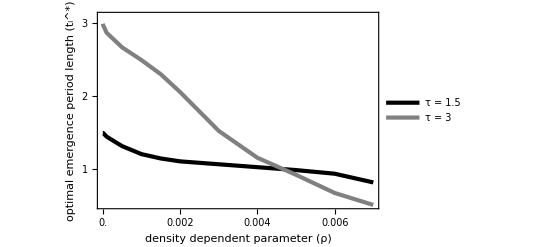

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[0,3,1],None},{{#,#,{0.03,0}}&/@Range[0,0.007,0.002],None}};
xx=ListLinePlot[{esslist0g,esslist0g3},Frame->{{True,True},{True,True}},PlotRange->{{0,0.007},{0.5,3.1}},FrameTicks->ftrange,PlotStyle->{{Black,AbsoluteThickness[3]},{Gray,AbsoluteThickness[3]}},FrameStyle->Directive[Black,Thick],FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["optimal emergence\n period length (t_l^*)",16,FontFamily->"Helvetica"],None},{Style["density dependent parameter (ρ)",16,FontFamily->"Helvetica"],None}},RotateLabel->True,PlotLegends->{Style["τ = 1.5",16],Style["τ = 3",16]}]
```